```mathematica
Inverse kinematics of 3-link planar robot arm
Keitaro Naruse
University of Aizu，Japan
```

```mathematica
(*Robot arm parameters*)
L1=1;L2=1;L3=1;
```

```mathematica
(*Forward kinematics function*)
FK[q_]:=
Module[{p0, p1, p2, p3},
p0 = {0,0,0};
p1 = p0+{L1 Cos[q[[1]]],L1 Sin[q[[1]]],q[[1]]};
p2 = p1+{L2 Cos[q[[1]]+q[[2]]],L2 Sin[q[[1]]+q[[2]]],q[[2]]};
p3 = p2+{L3 Cos[q[[1]]+q[[2]]+q[[3]]],L3 Sin[q[[1]]+q[[2]]+q[[3]]],q[[3]]};
{p0,p1, p2, p3}
];
```

```mathematica
(*Jacobian*)
J[q_]:={
{-L1 Sin[q[[1]]]-L2 Sin[q[[1]]+q[[2]]]-L3 Sin[q[[1]]+q[[2]]+q[[3]]],
-L2 Sin[q[[1]]+q[[2]]]-L3 Sin[q[[1]]+q[[2]]+q[[3]]],
-L3 Sin[q[[1]]+q[[2]]+q[[3]]]},
{L1 Cos[q[[1]]]+L2 Cos[q[[1]]+q[[2]]]+L3 Cos[q[[1]]+q[[2]]+q[[3]]],L2 Cos[q[[1]]+q[[2]]]+L3 Cos[q[[1]]+q[[2]]+q[[3]]],
L3 Cos[q[[1]]+q[[2]]+q[[3]]]},
{1,1,1}
};
```

```mathematica
(*Inverse kinematics solution: initialize*)
k = 0.1;
q={0.1, 0.2, 0.3};
pd = {1, 1, π/2};
```

```mathematica
(*Inverse kinematics solution: loop*)
For[i=1,i<50,i++,
p = FK[q];
q += k Inverse[J[q]].(pd - p[[4]])
]
```

```mathematica
(*Inverse kinematics solution: final*)
p = FK[q];
p[[4]]
```

{1.00726,0.999121,1.56524}

```mathematica
(*Inverse kinematics function*)
IK[pd_,q0_,k_]:=
Module[{p,q=q0},
For[i=1,i<=50,i++,
p = FK[q];
q += k Inverse[J[q]].(pd - p[[4]]);
];
q]
```

```mathematica
(*Inverse kinematics solution: initialize*)
k = 0.1;
q0={0.1, 0.2, 0.3};
pd = {1, 1, π/2};
```

```mathematica
(*Inverse kinematics solution by function*)
q=IK[pd,q0,0.1]
```

{-1.04709,2.09263,0.520258}

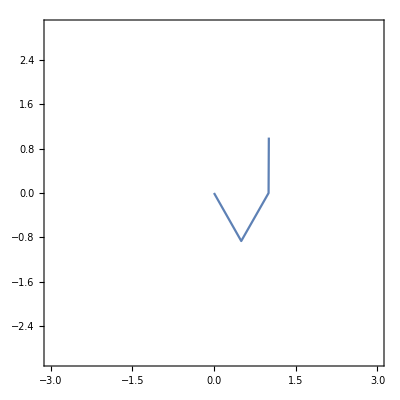

```mathematica
(*Draw a robot arm*)
(*Calculate forward kinematics*)
p = FK[q];
ListPlot[{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1]
```

```mathematica
k = 0.1;
q={0.1, 0.2, 0.3};
Manipulate[
(*Hand target pose*)
pd={xd, yd, qd};
(*Current robot arm pose *)
(*p = FK[q];*)
q=IK[pd,q,0.1];
p = FK[q];
ListPlot[{{p[[1,1;;2]], p[[2,1;;2]], p[[3,1;;2]], p[[4,1;;2]]},{pd[[1;;2]],pd[[1;;2]]+{Cos[qd],Sin[qd]}}},
Joined->True,
PlotRange->{{-3,3},{-3,3}},
Frame->True,
AspectRatio->1],
{{xd,0},-3,3},{{yd,0},-3,3},{{qd,0},-π,π}]
```